ParametricFunction[<>]

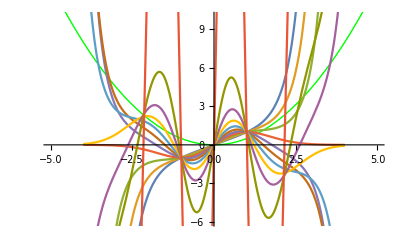

```mathematica
(*Schrodinger Equation solution for harmonic potential - parametric solution*)
ℏ=e=m0=1.;ω=1;
U[x_]:=1/2 m0 ω^2 x^2
pfun1=ParametricNDSolveValue[{-(ℏ^2/(2 m0)) ψ''[x]+U[x] ψ[x]==Ei ψ[x],ψ[0.]==0.,ψ[1.]==1.},ψ,{x,-4,4},{Ei}]
Show[Plot[U[x],{x,-5,5},PlotStyle->Directive[Thick,Green]],Plot[Evaluate@Table[Re[pfun1[Ei][x]],{Ei,0.,5.,0.5}],{x,-4,4}],PlotRange->{All,{-6,10}}]
```

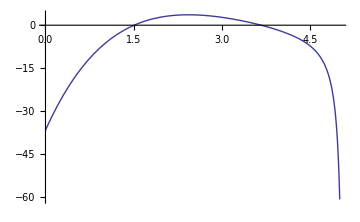

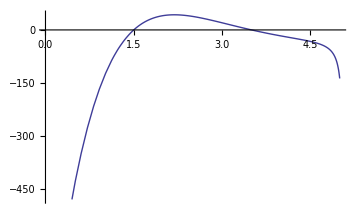

InterpolatingFunction::dmval: Input value {-5} lies outside the range of data in the interpolating function. Extrapolation will be used.

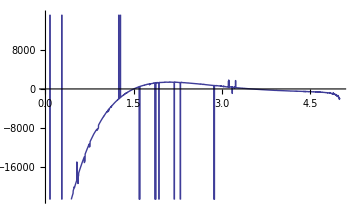

```mathematica
Plot[pfun1[Ei][-3],{Ei,0,5},ImageSize->Medium]
Plot[pfun1[Ei][-4],{Ei,0,5},ImageSize->Medium]
Plot[pfun1[Ei][-5],{Ei,0,5},ImageSize->Medium]
```

```mathematica
val=Map[FindRoot[pfun1[Ei][-4],{Ei,#}]&,{1,2,3}]
```

{{Ei→1.50001},{Ei→1.50001},{Ei→3.50169}}

ParametricFunction[<>]

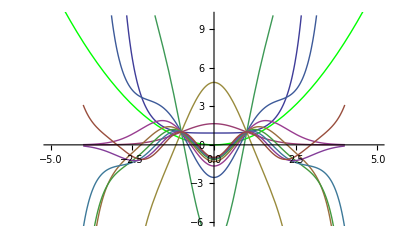

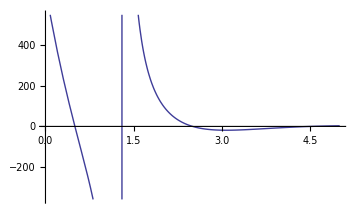

```mathematica
pfun2=ParametricNDSolveValue[{-(ℏ^2/(2 m0)) ψ''[x]+U[x] ψ[x]==Ei ψ[x],ψ'[0.]==0.,ψ[1.]==1.},ψ,{x,-4,4},{Ei}]
Show[Plot[U[x],{x,-5,5},PlotStyle->Directive[Thick,Green]],Plot[Evaluate@Table[Re[pfun2[Ei][x]],{Ei,0.,5.,0.5}],{x,-4,4}],PlotRange->{All,{-6,10}}]
Plot[pfun2[Ei][-4],{Ei,0,5},ImageSize->Medium]
```

```mathematica
val1=Map[FindRoot[pfun1[Ei][-4],{Ei,#}]&,{1,2,3}]
val2=Map[FindRoot[pfun2[Ei][-4],{Ei,#}]&,{1,2,3}]
```

{{Ei→1.50001},{Ei→1.50001},{Ei→3.50169}}

{{Ei→0.5},{Ei→2.5002},{Ei→2.5002}}

```mathematica
eigenEv=val1/.Rule[_,x_]->x//Flatten;
eigenOd=val2/.Rule[_,x_]->x//Flatten;
Sort[Join[eigenEv,eigenOd]]
```

{0.5,1.50001,1.50001,2.5002,2.5002,3.50169}

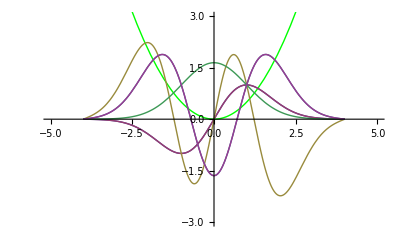

```mathematica
Show[Plot[U[x],{x,-5,5},PlotStyle->Directive[Thick,Green]],Plot[Evaluate@{Table[Re[pfun1[Ei][x]],{Ei,eigenEv}],Table[Re[pfun2[Ei][x]],{Ei,eigenOd}]},{x,-4,4}],PlotRange->{All,{-3,3}}]
```